```mathematica
Clear["Global`*"]
```

```mathematica
HA=ℏ({{ωr, 0, 0}, {0, ωe, 0}, {0, 0, ωg}});
HAF=ℏ/2({{0, Ω2 E^(-I ω2 t), 0}, {Conjugate[Ω2] E^(I ω2 t), 0, Ω1 E^(-I ω1 t)}, {0, Conjugate[Ω1] E^(I ω1 t), 0}});
U=({{E^(-ⅈ(ω1+ω2)t), 0, 0}, {0, E^(-I ω1 t), 0}, {0, 0, 1}});
```

```mathematica
ℏ MatrixForm[FullSimplify[1/ℏ(ConjugateTranspose[U].(HA+HAF).U-I ℏ ConjugateTranspose[U].D[U,t]),{t>0,ω1∈Reals,ω2∈Reals}]]
```

ℏ (-ω1-ω2+ωr | Ω2/2 | 0
Conjugate[Ω2]/2 | -ω1+ωe | Ω1/2
0 | Conjugate[Ω1]/2 | ωg)

```mathematica
Htilde=ℏ ({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}});
ρ=({{σgg[t], σge[t], σgr[t]}, {σeg[t], σee[t], σer[t]}, {σrg[t], σre[t], σrr[t]}});
```

```mathematica
MatrixForm[D[ρ,t]]
```

(σgg'[t] | σge'[t] | σgr'[t]
σeg'[t] | σee'[t] | σer'[t]
σrg'[t] | σre'[t] | σrr'[t])

```mathematica
MatrixForm[({{σgg'[t], σge'[t], σgr'[t]}, {σeg'[t], σee'[t], σer'[t]}, {σrg'[t], σre'[t], σrr'[t]}})]==MatrixForm[FullSimplify[1/(I ℏ)(ℏ ({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}}).ρ-ρ.({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}})ℏ)]]
```

(σgg'[t] | σge'[t] | σgr'[t]
σeg'[t] | σee'[t] | σer'[t]
σrg'[t] | σre'[t] | σrr'[t])==(-1/2 ⅈ Ω1 (σeg[t]-σge[t]) | -1/2 ⅈ (Ω1 σee[t]+2 Δe σge[t]-Ω1 σgg[t]-Ω2 σgr[t]) | -1/2 ⅈ (Ω1 σer[t]-Ω2 σge[t]+2 Δr σgr[t])
1/2 ⅈ (Ω1 σee[t]+2 Δe σeg[t]-Ω1 σgg[t]-Ω2 σrg[t]) | 1/2 ⅈ (Ω1 σeg[t]+Ω2 σer[t]-Ω1 σge[t]-Ω2 σre[t]) | 1/2 ⅈ (Ω2 σee[t]+2 (Δe-Δr) σer[t]-Ω1 σgr[t]-Ω2 σrr[t])
1/2 ⅈ (-Ω2 σeg[t]+Ω1 σre[t]+2 Δr σrg[t]) | -1/2 ⅈ (Ω2 σee[t]+2 (Δe-Δr) σre[t]-Ω1 σrg[t]-Ω2 σrr[t]) | -1/2 ⅈ Ω2 (σer[t]-σre[t]))

```mathematica
NDSolve[{({{σgg'[t], σge'[t], σgr'[t]}, {σeg'[t], σee'[t], σer'[t]}, {σrg'[t], σre'[t], σrr'[t]}})==1/(I ℏ)(ℏ ({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}}).ρ-ρ.({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}})ℏ),σgg[0]==1,σee[0]==0,σrr[0]==0,σge[0]==0,σgr[0]==0,σer[0]==0,σeg[0]==0,σrg[0]==0,σre[0]==0},{σgg[t],σee[t],σrr[t]},{t,0,2}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{{{σgg'[t],σge'[t],σgr'[t]},{σeg'[t],σee'[t],σer'[t]},{σrg'[t],σre'[t],σrr'[t]}}=={{-(ⅈ (1/2 Ω1 ℏ σeg[t]-1/2 Ω1 ℏ σge[t]))/ℏ,-(ⅈ (1/2 Ω1 ℏ σee[t]-ℏ (-Δe σge[t]+1/2 Ω1 σgg[t]+1/2 Ω2 σgr[t])))/ℏ,-(ⅈ (1/2 Ω1 ℏ σer[t]-ℏ (1/2 Ω2 σge[t]-Δr σgr[t])))/ℏ},{-(ⅈ (-1/2 Ω1 ℏ σee[t]+ℏ (-Δe σeg[t]+1/2 Ω1 σgg[t]+1/2 Ω2 σrg[t])))/ℏ,-(ⅈ (-ℏ (-Δe σee[t]+1/2 Ω1 σeg[t]+1/2 Ω2 σer[t])+ℏ (-Δe σee[t]+1/2 Ω1 σge[t]+1/2 Ω2 σre[t])))/ℏ,-(ⅈ (-ℏ (1/2 Ω2 σee[t]-Δr σer[t])+ℏ (-Δe σer[t]+1/2 Ω1 σgr[t]+1/2 Ω2 σrr[t])))/ℏ},{-(ⅈ (-1/2 Ω1 ℏ σre[t]+ℏ (1/2 Ω2 σeg[t]-Δr σrg[t])))/ℏ,-(ⅈ (ℏ (1/2 Ω2 σee[t]-Δr σre[t])-ℏ (-Δe σre[t]+1/2 Ω1 σrg[t]+1/2 Ω2 σrr[t])))/ℏ,-(ⅈ (ℏ (1/2 Ω2 σer[t]-Δr σrr[t])-ℏ (1/2 Ω2 σre[t]-Δr σrr[t])))/ℏ}},σgg[0]==1,σee[0]==0,σrr[0]==0,σge[0]==0,σgr[0]==0,σer[0]==0,σeg[0]==0,σrg[0]==0,σre[0]==0},{σgg[t],σee[t],σrr[t]},{t,0,2}]

```mathematica
Solve[{ ({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})==1/(I ℏ)(ℏ ({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}}).({{σgg, σge, σgr}, {Conjugate[σge], σee, σer}, {Conjugate[σgr], Conjugate[σer], σrr}})-({{σgg, σge, σgr}, {Conjugate[σge], σee, σer}, {Conjugate[σgr], Conjugate[σer], σrr}}).({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}})ℏ)},{σgg,σrr,σee,σge,σgr,σer}]
```

$Aborted

```mathematica
Clear[Δr]
```

{cg[t]→ParametricFunction[<>],ce[t]→ParametricFunction[<>],cr[t]→ParametricFunction[<>]}

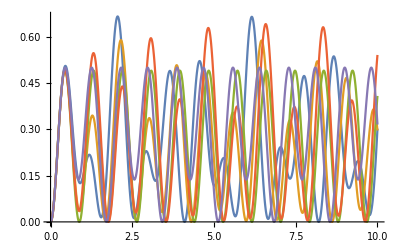

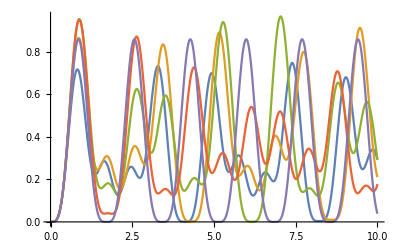

```mathematica
Ω1=5;
Ω2=5;
Δe=1;
ℏ=1;
sol=ParametricNDSolve[{({{cr'[t]}, {ce'[t]}, {cg'[t]}})==ℏ/(I ℏ)({{-Δr, Ω2/2, 0}, {Ω2/2, -Δe, Ω1/2}, {0, Ω1/2, 0}}).({{cr[t]}, {ce[t]}, {cg[t]}}),cg[0]==1,ce[0]==0,cr[0]==0},{cg[t],ce[t],cr[t]},{t,0,10},{Δr}]
Plot[Evaluate[Table[Conjugate[ce[t][Δr]]ce[t][Δr]/.sol,{Δr,-2,2,1}]],{t,0,10},PlotRange->Full]
Plot[Evaluate[Table[Conjugate[cr[t][Δr]]cr[t][Δr]/.sol,{Δr,-2,2,1}]],{t,0,10},PlotRange->Full]
```

```mathematica
Evaluate[Abs[cg[t][3]]^2/.sol]
```

Abs[InterpolatingFunction[{{0., 10.}}, <>][t]]^2